```mathematica
Clear["Global`*"]
Column@NotebookEvaluate[FileNameJoin[{NotebookDirectory[],"../../../../mathematica_plot_options.nb"}]]
```

Column[Null]

```mathematica
Table[name[t]="/Users/tomoaki/BEM/Tonegawa2024_DT0d025_ELEMlinear_ALEquasi_quad_ALEPERIOD1_T"<>StringReplace[ToString[t],"."->"d"]<>"/result.json",{t,0.65,0.5,-0.01}]
Do[data[t]=Import@name[t],{t,0.65,0.5,-0.01}]
jsonInfo[name[0.52]]
```

{/Users/tomoaki/BEM/Tonegawa2024_DT0d025_ELEMlinear_ALEquasi_quad_ALEPERIOD1_T0d65/result.json,/Users/tomoaki/BEM/Tonegawa2024_DT0d025_ELEMlinear_ALEquasi_quad_ALEPERIOD1_T0d64/result.json,/Users/tomoaki/BEM/Tonegawa2024_DT0d025_ELEMlinear_ALEquasi_quad_ALEPERIOD1_T0d63/result.json,/Users/tomoaki/BEM/Tonegawa2024_DT0d025_ELEMlinear_ALEquasi_quad_ALEPERIOD1_T0d62/result.json,/Users/tomoaki/BEM/Tonegawa2024_DT0d025_ELEMlinear_ALEquasi_quad_ALEPERIOD1_T0d61/result.json,/Users/tomoaki/BEM/Tonegawa2024_DT0d025_ELEMlinear_ALEquasi_quad_ALEPERIOD1_T0d6/result.json,/Users/tomoaki/BEM/Tonegawa2024_DT0d025_ELEMlinear_ALEquasi_quad_ALEPERIOD1_T0d59/result.json,/Users/tomoaki/BEM/Tonegawa2024_DT0d025_ELEMlinear_ALEquasi_quad_ALEPERIOD1_T0d58/result.json,/Users/tomoaki/BEM/Tonegawa2024_DT0d025_ELEMlinear_ALEquasi_quad_ALEPERIOD1_T0d57/result.json,/Users/tomoaki/BEM/Tonegawa2024_DT0d025_ELEMlinear_ALEquasi_quad_ALEPERIOD1_T0d56/result.json,/Users/tomoaki/BEM/Tonegawa2024_DT0d025_ELEMlinear_ALEquasi_quad_ALEPERIOD1_T0d55/result.json,/Users/tomoaki/BEM/Tonegawa2024_DT0d025_ELEMlinear_ALEquasi_quad_ALEPERIOD1_T0d54/result.json,/Users/tomoaki/BEM/Tonegawa2024_DT0d025_ELEMlinear_ALEquasi_quad_ALEPERIOD1_T0d53/result.json,/Users/tomoaki/BEM/Tonegawa2024_DT0d025_ELEMlinear_ALEquasi_quad_ALEPERIOD1_T0d52/result.json,/Users/tomoaki/BEM/Tonegawa2024_DT0d025_ELEMlinear_ALEquasi_quad_ALEPERIOD1_T0d51/result.json,/Users/tomoaki/BEM/Tonegawa2024_DT0d025_ELEMlinear_ALEquasi_quad_ALEPERIOD1_T0d5/result.json}

no. | title | length
1 | cpu_time | 401
2 | eq_of_motion | 401
3 | float_COM | 401
4 | float_EK | 401
5 | float_EP | 401
6 | float_accel | 401
7 | float_area | 401
8 | float_drag_force | 401
9 | float_drag_torque | 401
10 | float_force | 401
11 | float_pitch | 401
12 | float_roll | 401
13 | float_torque | 401
14 | float_velocity | 401
15 | float_yaw | 401
16 | gradPhi_worst_grad | 401
17 | gradPhi_worst_iteration | 401
18 | gradPhi_worst_value | 401
19 | simulation_time | 401
20 | wall_clock_time | 401
21 | water_E | 401
22 | water_EK | 401
23 | water_EP | 401
24 | water_face_size | 401
25 | water_point_size | 401
26 | water_volume | 401

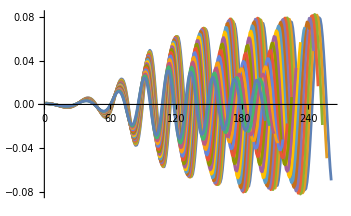

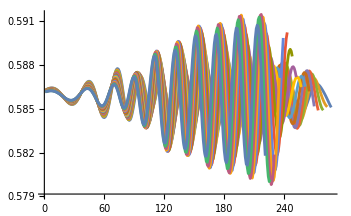

```mathematica
findFirst[data_,condition_]:=Module[{list,ret},
list="simulation_time"/.data;
ret=Length[list];
Return [ret];
]

indices[data_,{s_,e_}_:{5,10}]:=Module[{list,len,startIndex,endIndex},
list="simulation_time"/.data;
len=Length[list];
startIndex=Position[list,x_/;x>s];
If[startIndex=={},startIndex=len,startIndex=startIndex[[1,1]]];
endIndex=Position[list,x_/;x>e];
If[endIndex=={},endIndex=len,endIndex=endIndex[[1,1]]];
startIndex;;endIndex
];

extractFourier[dataIN_,{s_,e_}_:{5,10},title_:"float_pitch",n_:0]:=Module[{end,data,x,y,span},
span=indices[dataIN,{s,e}];
x=("simulation_time"/.dataIN)[[span]];
If[n==0,y=(title/.dataIN)[[span]],y=((title/.dataIN)[[span]])[[;;,n]]];
interpolateAndFourier[x,y]
]


ListPlot[Table[("float_pitch"/.data[T])[[indices[data[T],{2,2+10*T}]]],{T,0.65,0.5,-0.01}],Joined->True,PlotRange->All]
ListPlot[Table[("float_COM"/.data[T])[[indices[data[T],{2,2+11*T}]]][[;;,3]],{T,0.65,0.5,-0.01}],Joined->True,PlotRange->All]
```

```mathematica
list=Table[i,{i,0.65,0.5,-0.01}]
Manipulate[
{
legend={};
ListPlot[
Table[AppendTo[legend,T];{1/#1,180/(2π)#2}&@@@extractFourier[data[T],{2,2+a*T},"float_pitch"][[2;;]],{T,list}]
,Joined->True
,PlotRange->{{0.3,0.9},All}
,Evaluate[plot2Doption]
,PlotLabel->"Pitch"
,FrameLabel->{"Time [s]","Pitch [°]"}
,PlotStyle->Table[{ColorData["DarkRainbow"][0.1*i]},{i,1,10,1}]
,PlotLegends->legend]
,
ListPlot[
Table[{1/#1,#2}&@@@extractFourier[data[T],{2,2+a*T},"float_COM",3][[2;;]],{T,list}]
,Joined->True
,PlotRange->{{0.3,0.9},All}
,Evaluate[plot2Doption]
,PlotLabel->"Heave"
,FrameLabel->{"Time [s]","Heave [m]"}
,PlotStyle->Table[{ColorData["DarkRainbow"][0.1*i]},{i,1,10,1}]
,PlotLegends->legend
]
}
,{a,11,11,0.1}]

Manipulate[
{
legend={};
ListContourPlot[
Flatten[Table[AppendTo[legend,T];{1/#1,T,180/(2π)#2}&@@@extractFourier[data[T],{2,2+a*T},"float_pitch"][[2;;]],{T,list}],1]
,PlotRange->{{0.3,0.9},{0.5,0.65},All}
,FrameLabel->{"Heave Period [s]","Incident Wave Period [s]"}
,ImageSize->Medium
,Evaluate[plot3Doption]
]
,
ListContourPlot[
Flatten[Table[{1/#1,T,#2}&@@@extractFourier[data[T],{2,2+a*T},"float_COM",3][[2;;]],{T,list}],1]
,PlotRange->{{0.3,0.9},{0.5,0.65},All}
,FrameLabel->{"Heave Period [s]","Incident Wave Period [s]"}
,Evaluate[plot3Doption]
,ImageSize->Medium
,InterpolationOrder->3]
}
,{a,11,11,0.1}]

Print["図の見た方：浮体のピッチは単純なsin関数ではなく，様々な周期のsin,cos関数の和となっている．この図は，:3042:308b:5165:5c04:6ce2:306b:5bfe:3059:308b:30d4:30c3:30c1:52d5:63faにおいて，よく揺れた成分を示している"]
```

{0.65,0.64,0.63,0.62,0.61,0.6,0.59,0.58,0.57,0.56,0.55,0.54,0.53,0.52,0.51,0.5}

図の見た方：浮体のピッチは単純なsin関数ではなく，様々な周期のsin,cos関数の和となっている．この図は，ある入射波に対するピッチ動揺において，よく揺れた成分を示している